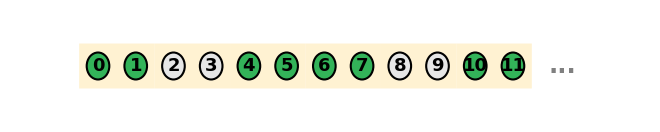

```mathematica
nBloques=6;
maxEntero=2 nBloques-1;

bloquesEnA={0,2,3,5}; (*n de los bloques P_n incluidos en el ejemplo A*)

colorEnA=RGBColor[0.2,0.7,0.35];
colorFueraA=RGBColor[0.9,0.9,0.9];
colorBloque=RGBColor[1,0.93,0.75];

cajasBloque=Table[{colorBloque,Opacity[0.7],Rectangle[{2 n-0.5,-0.5},{2 n+1.5,0.5},RoundingRadius->0.35]},{n,0,nBloques-1}];

puntos=Table[{If[MemberQ[bloquesEnA,Floor[k/2]],colorEnA,colorFueraA],Disk[{k,0},0.3],Black,AbsoluteThickness[1.5],Circle[{k,0},0.3],Text[Style[k,18,Bold,Black],{k,0}]},{k,0,maxEntero}];

puntosSuspensivos=Text[Style["...",24,Bold,Gray],{maxEntero+1.3,0}];

grafico=Graphics[{cajasBloque,puntos,puntosSuspensivos},PlotRange->{{-1,maxEntero+2.3},{-1.2,1.2}},ImageSize->660];

Legended[grafico,SwatchLegend[{colorBloque,colorEnA,colorFueraA},{"Bloque {2n,2n+1}","En A","Fuera de A"},LabelStyle->Directive[FontSize->16],LegendMarkerSize->20]]
```

```mathematica
Export["C:\\Users\\jesus\\Desktop\\Universidad\\Teoría de la probabilidad\\Latex_Teoria_Probabilidad\\imagenes\\problemas_Quesada\\prob_quesada_1_20_a.png",%51,"PNG"]
```

C:\Users\jesus\Desktop\Universidad\Teoría de la probabilidad\Latex_Teoria_Probabilidad\imagenes\problemas_Quesada\prob_quesada_1_20_a.png